# Vertical asymptote

```mathematica
ClearAll["Global`*"]
```

```mathematica
f[x_]=(x+3)/(x-1);
```

```mathematica
zero=Solve[Denominator[f[x]]==0,x]
```

{{x→1}}

```mathematica
Limit[f[x],x->zero[[1,1,2]]]
```

∞

```mathematica
verticalAsymptote=zero[[1,1,2]]
```

1

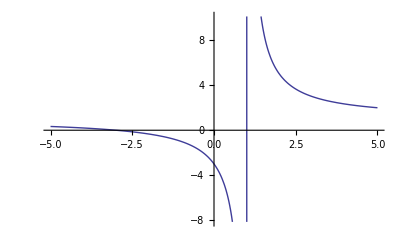

```mathematica
Plot[f[x],{x,-5,5}]
```